```mathematica
SetDirectory[NotebookDirectory[]];
SciFormFormat[mantissa_,base_,exponent_]:=mantissa<>"e"<>If[exponent=="","0",exponent]
SciForm[n_]:=ToString[ScientificForm[1.0 n,NumberFormat->SciFormFormat]]
```

```mathematica
files=FileNames[RegularExpression["pruebaCxx.+\\.csv"],"."];
files=SortBy[
files,
ToExpression@StringTake[#,15;;-5]&
];

names=StringSplit["xuv xdv xubar xdbar xgl"];
```

```mathematica
F[X_,{a,b,c,d,e,f,g}]:=a X^b(1-X)^c(1+d X+e X^2+f Log[X]+g Log[X]^2)
```

```mathematica
fitXY[x_,y_]:=NonlinearModelFit[{x,y}ᵀ,a X^b(1-X)^c(1+d X+e X^2+f Log[X]+g Log[X]^2),{
{a,3.92},
{b,0.288},
{c,4.82},
{d,0.0001},
{e,6.38},
{f,0.298},
{g,0.0492}
},X,Method->"PrincipalAxis"]

fit[name_]:=Block[{fit,data},
data=Import[name,"Table"][[2;;]]ᵀ;
AssociationThread[names->(fitXY[First[data],#]&/@Rest[data])]
]
```

## Fit

```mathematica
results=AssociationThread[files->Map[fit,files]]//Quiet;
```

```mathematica
results=KeyMap[SciForm@ToExpression@StringTake[#,15;;-5]&,results];
```

## Parameter examination

```mathematica
parameters = Map[
Map[Association[#["BestFitParameters"]]&],
results
];
parameters=Map[Map[KeyMap[ToString]],parameters];
Export["fit_parameters.json",parameters]
```

fit_parameters.json

```mathematica
df=Dataset[parameters];
```

```mathematica
SymLog10[x_]:=Sign[x]Log10[Abs[x]]
```

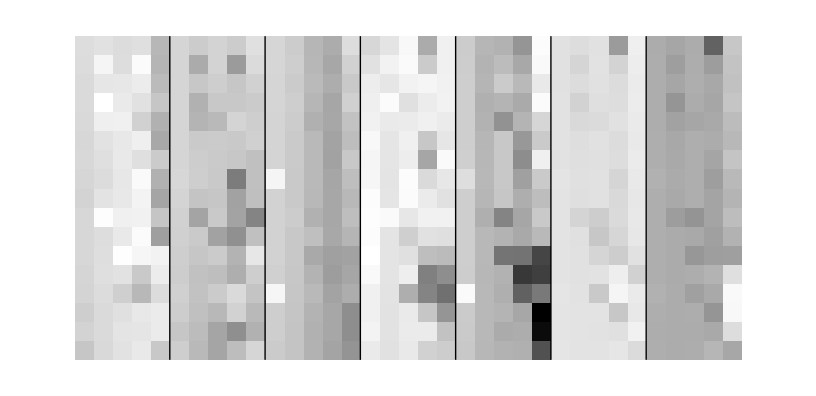

```mathematica
ArrayPlot[SymLog10@ArrayFlatten@{Normal@Values@Values@df[[All,All,#]]&/@{"a","b","c","d","e","f","g"}},Mesh->{None,6},MeshStyle->Black]
```

#### Residual examination

max_abs_residual.csv

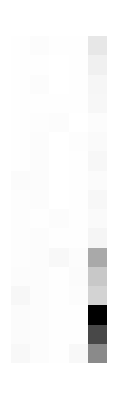

```mathematica
maxres=Map[
Map[Max@Abs@#["FitResiduals"]&],
results
];
Export["max_abs_residual.csv",Dataset[maxres]]
ArrayPlot[Values[Values/@maxres]]
```

## Plots

```mathematica
AnimationVideo[
ListLinePlot[
#["Data"]&/@Values[results[[i]]],
ScalingFunctions->{"Log",Automatic},
Frame->True,
PlotRange->{0,1},
ImageSize->400
],
{i,1,Length[results],1}
]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

Video[/home/niebla/Documents/Wolfram/Video/AnimationVideo-8aa2c156-cab1-4816-afbc-0bfc44360b4b.mp4,Appearance→Automatic,AudioOutputDevice→Automatic,SoundVolume→Automatic]/home/niebla/Documents/Wolfram/Video/AnimationVideo-8aa2c156-cab1-4816-afbc-0bfc44360b4b.mp4Basic1StandardForm

```mathematica
Animate[
ListLinePlot[
#["Data"]&/@Values[results[[i]]],
ScalingFunctions->{"Log",Automatic},
Frame->True,
PlotRange->{0,1},
ImageSize->400
],
{i,1,Length[results],1}
]
```

```mathematica
plots=Map[
Map[
Show[
ListLinePlot[#["Data"],Frame->True,PlotStyle->Red,PlotRange->All,ScalingFunctions->{"Log",Automatic}],
Plot[#[t],{t,0.0005,1},PlotStyle->Directive[Opacity[1,Black],Dashed],PlotRange->All,ScalingFunctions->{"Log",Automatic}]
]&
],
results
];
```

```mathematica
Dataset[plots]
```